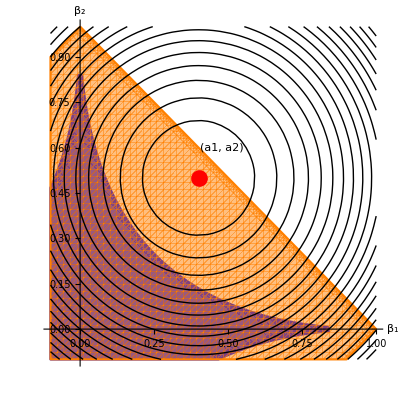

```mathematica
Clear["Global`*"]
a1=0.4;
a2=0.5;
f[x_,y_]:=-(a1 x + a2 y)+1/2 (x^2+y^2);
g1[x_,y_,q_]:=Abs[x]^q+Abs[y]^q;
g2[x_,y_,q_]:=(Abs[x]+Abs[y])^q;
g3[x_,y_]:=Abs[x]+Abs[y];

t=1;
q=1/2;

pg1=RegionPlot[g1[x,y,q]≤ t,{x,-0.1,1},{y,-0.1,1},
AxesLabel->{Subscript[β,1],Subscript[β,2],"t"},
Frame->None,
AxesOrigin->{0,0},
Axes->True,
BoundaryStyle->{Blue},
PlotStyle->{Blue,Opacity[0.8]},
PlotPoints->50
];
pg2=RegionPlot[g2[x,y,q]≤ t,{x,-0.1,1},{y,-0.1,1},
AxesLabel->{Subscript[β,1],Subscript[β,2],"t"},
Frame->None,
AxesOrigin->{0,0},
Axes->True,
BoundaryStyle->{Orange},
PlotStyle->{Orange,Opacity[0.5]},
PlotPoints->50
];
pg3=RegionPlot[g3[x,y]≤ t^(1/q),{x,-0.1,1},{y,-0.1,1},
AxesLabel->{Subscript[β,1],Subscript[β,2],"t"},
Frame->None,
AxesOrigin->{0,0},
Axes->True,
BoundaryStyle->{Green},
PlotStyle->{Green,Opacity[0.25]},
PlotPoints->50
];
pf=ContourPlot[f[x,y],{x,-0.1,1},{y,-0.1,1},
Contours->20,
ContourShading->None,
ContourStyle->Thick,
Frame->None,
AxesOrigin->{0,0},
Axes->True
];
Show[pg1,pg2,pf,
Epilog->{
PointSize[0.03],Red,Point[{a1,a2}],Black,Text["(a1, a2)",{a1,a2}*1.2]
}]
```

```mathematica
(* Univariate *)
Clear["Global`*"]
f[x_,a_]:=-a x + 1/2 x^2;
g[x_,q_]:=Abs[x]^q;

Manipulate[
pg=RegionPlot[g[x,q]≤ t,{x,-1.25,1.25},{y,-0.75, 1.5},
PlotLabel->"q = "<>ToString[N[q]]<>", a = "<>ToString[N[a]]<>", t = "<>ToString[N[t]],
Frame->None,
AxesOrigin->{0,0},
Axes->True,
PlotStyle->{Opacity[0.25]}
];
pf=Plot[f[x,a],{x,-1.25,1.25},
PlotStyle->{Black,Thick}
];
Show[pg,pf],
{{q,1/2},0,2,0.1},
{{a,1},-2,2,0.1},
{{t,1},0,5,0.1}]
```

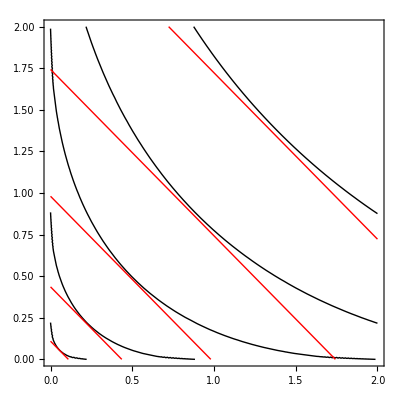

(x==0&&(y==0||Re[y]<0||(Im[y]≠0&&Re[y]==0)||Re[y]>0))||(Re[x]<0&&(y==0||Re[y]<0||(Im[y]≠0&&Re[y]==0)||Re[y]>0))||(Im[x]≠0&&Re[x]==0&&(y==0||Re[y]<0||(Im[y]≠0&&Re[y]==0)||Re[y]>0))||(Re[x]>0&&(y==0||Re[y]<0||(Im[y]≠0&&Re[y]==0)||Re[y]>0))

```mathematica
p1=ContourPlot[x^(1/2)+y^(1/2),{x,0,2},{y,0,2},
Contours->5,
ContourShading->None,
ContourStyle->Black];
p2=ContourPlot[(x+y)^(1/2),{x,0,2},{y,0,2},
Contours->5,
ContourShading->None,
ContourStyle->Red];
Show[p1,p2]
```

```mathematica
Minimize[{-βOLS *β+1/2β^2,},β]
```

{-βOLS^2/2,{β→βOLS}}